v2: updated version following notes, plus Mean-field
v3: mean-field (more) + ϵ implementation, bsp

v4: mean-field corrected

v5: mean-field zero solutions
v5-check: check why zero solutions

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
MatX[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δx)(IdentityMatrix[2]+ I λR PauliMatrix[2] +I λD PauliMatrix[1]) + (1-δx)Exp[I k.a1](IdentityMatrix[2]- I λR PauliMatrix[2] -I λD PauliMatrix[1])];
```

```mathematica
MatY[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δy)(IdentityMatrix[2]- I λR PauliMatrix[1] +I λD PauliMatrix[2]) + (1-δy)Exp[I k.a2](IdentityMatrix[2]+ I λR PauliMatrix[1] -I λD PauliMatrix[2])];
```

```mathematica
Clear[hamLieb];hamLieb[bsp_,k_] := hamLieb[bsp,k] = Module[{λ = bsp[[1]], δ = bsp[[2]], ϵ = bsp[[3]]},Module[ {mx = MatX[λ,δ,k],my = MatY[λ,δ,k] },ArrayFlatten[ {{-ϵ IdentityMatrix[2],mx,my},{mx†,0,0},{my†,0,0}} ]]];
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},hamLieb[bsp,k]]//MatrixForm
```

(-0.1 | 0. | 1.89671-0.0384992 ⅈ | 0.228656+1.27618 ⅈ | 0.79532+0.812485 ⅈ | 0.825983-0.705407 ⅈ
0. | -0.1 | -0.277952+1.26636 ⅈ | 1.89671-0.0384992 ⅈ | -1.03328+0.334945 ⅈ | 0.79532+0.812485 ⅈ
1.89671+0.0384992 ⅈ | -0.277952-1.26636 ⅈ | 0 | 0 | 0 | 0
0.228656-1.27618 ⅈ | 1.89671+0.0384992 ⅈ | 0 | 0 | 0 | 0
0.79532-0.812485 ⅈ | -1.03328-0.334945 ⅈ | 0 | 0 | 0 | 0
0.825983+0.705407 ⅈ | 0.79532-0.812485 ⅈ | 0 | 0 | 0 | 0)

```mathematica
Clear[EnerLieb];EnerLieb[bsp_,k_] := EnerLieb[bsp,k]= Chop[  N[Sort[Eigenvalues[hamLieb[bsp,k] ]]] ];
Clear[ULieb];ULieb[bsp_,k_] :=ULieb[bsp,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[bsp,k] ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},ULieb[bsp,k]]//MatrixForm
```

(-0.291697-0.410239 ⅈ | -0.144222+0.483392 ⅈ | 0 | 0 | 0.141667-0.47483 ⅈ | -0.287776-0.404724 ⅈ
-0.404481+0.299631 ⅈ | -0.486108-0.134781 ⅈ | 0 | 0 | 0.477498+0.132394 ⅈ | -0.399043+0.295603 ⅈ
-0.0448482+0.1143 ⅈ | 0.0878943-0.605719 ⅈ | -0.268285-0.133488 ⅈ | -0.0249474+0.340796 ⅈ | 0.0894792-0.616641 ⅈ | 0.0454593-0.115857 ⅈ
0.419659-0.224763 ⅈ | 0.0827746-0.0234278 ⅈ | -0.129963+0.532826 ⅈ | -0.423975+0.211893 ⅈ | 0.0842672-0.0238503 ⅈ | -0.425377+0.227826 ⅈ
0.0721844+0.366197 ⅈ | 0.036761-0.172203 ⅈ | 0.69932+0.346932 ⅈ | -0.0892841-0.192446 ⅈ | 0.0374239-0.175308 ⅈ | -0.0731681-0.371187 ⅈ
0.334985 | 0.279354 | 0 | 0.78331 | 0.284391 | -0.339549)

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[bsp_] := Table[ EnerLieb[bsp,k]  ,{k,kCut} ];
```

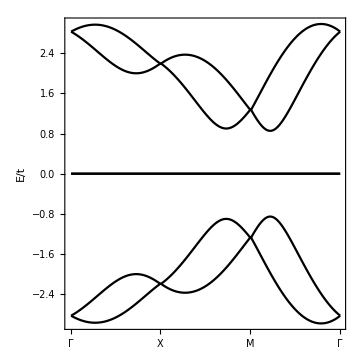

```mathematica
Block[ {bsp={{0.0,0.45},{0.0,0.0},0}},ListPlot[Table[ PlotDispData[bsp][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean Field Theory

Here nup, ndn, splus and sdown are all 3 vectors (for A, B, C)

Follow Eq. 5 of ref https://arxiv.org/pdf/2110.03813.pdf

```mathematica
IJMat[i_,j_]:= ArrayFlatten[ Table[ If[i1==i&&j1==j,1,0],{i1,1,6},{j1,1,6}]];
```

MF vec = { n_(A↑), n_(B↑), n_(C↑), n_(A↓), n_(B↓),n_(C↓), (S^+)_A, (S^+)_B, (S^+)_C, (S^-)_A, (S^-)_B, (S^-)_C}

```mathematica
MFMatvec = {IJMat[2,2],IJMat[4,4], IJMat[6,6], IJMat[1,1],IJMat[3,3], IJMat[5,5], -IJMat[2,1],-IJMat[4,3],-IJMat[6,5],-IJMat[1,2],-IJMat[3,4],-IJMat[5,6]};
```

```mathematica
MFMatvecConj = {IJMat[1,1],IJMat[3,3], IJMat[5,5],IJMat[2,2],IJMat[4,4], IJMat[6,6],IJMat[1,2],IJMat[3,4],IJMat[5,6] , IJMat[2,1],IJMat[4,3],IJMat[6,5]};
```

```mathematica
Clear[HamMFU];HamMFU[MFvec_]:= HamMFU[MFvec] = MFvec.MFMatvec;
```

```mathematica
Clear[HamMFull];HamMFull[bsp_,MFvec_,k_,U_]:= HamMFull[bsp,MFvec,k,U]= hamLieb[bsp,k] +U HamMFU[MFvec];
```

```mathematica
Clear[EnerMF];EnerMF[bsp_,MFvec_,k_,U_] := EnerMF[bsp,MFvec,k,U]= Chop[  N[Sort[Eigenvalues[HamMFull[bsp,MFvec,k,U] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[bsp_,MFvec_,k_,U_] :=ULiebMF[bsp,MFvec,k,U]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[HamMFull[bsp,MFvec,k,U]  ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Clear[MFvalue];MFvalue[bsp_,MFvec_,U_,μ_,β_,krange_] :=MFvalue[bsp,MFvec,U,μ,β,krange]=Table[1/Length[kSpan[krange]] Chop[Sum[ Module[{um = ULiebMF[bsp,MFvec,k,U]}, Fermi[β, EnerMF[bsp,MFvec,k,U][[band]] -μ](um†.MFMatvecConj[[mfvectors]].um)[[band,band]]],{band,1 ,6},{k,kSpan[krange]}]],{mfvectors,1,12}];
```

```mathematica
Clear[NumEq];NumEq[bsp_,MFvec_,U_,μ_,β_,krange_] :=NumEq[bsp,MFvec,U,μ,β,krange]=1/Length[kSpan[krange]] Chop[Sum[ Fermi[β, EnerMF[bsp,MFvec,k,U][[band]] -μ],{band,1 ,6},{k,kSpan[krange]}]];
```

```mathematica
Clear[FindMu];FindMu[bsp_,MFvec_,U_,fil_,β_,krange_] :=FindMu[bsp,MFvec,U,fil,β,krange]=μ/.FindRoot[ NumEq[bsp,MFvec,U,μ,β,krange]-fil,{μ,-3-U,3+U },Method-> "Secant",Evaluated->False, PrecisionGoal->3];
```

```mathematica
ItrFnMF[bsp_,U_,fil_,β_,krange_]:=  NestList[ {FindMu[bsp,#[[2]],U,fil,β,krange],MFvalue[bsp,#[[2]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,12]},10][[10]];
```

```mathematica
ItrFnMFCheck[bsp_,U_,fil_,β_,krange_]:=   NestList[ {FindMu[bsp,#[[2]],U,fil,β,krange],MFvalue[bsp,#[[2]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,12]},10];
```

#### Try 2: mean-field

```mathematica
Clear[ItrFnMFMu];ItrFnMFMu[bsp_,U_,μ_,β_,krange_]:=  ItrFnMFMu[bsp,U,μ,β,krange]=NestList[ MFvalue[bsp,#,U,μ,β,krange]&,RandomReal[1,12],10][[10]];
```

```mathematica
Clear[NumEqv2];NumEqv2[MFvec_] :=NumEqv2[MFvec]=Total[ MFvec[[1;;6]] ];
```

```mathematica
Clear[FindMuAfter];FindMuAfter[bsp_,U_,fil_,β_,krange_]:= FindMuAfter[bsp,U,fil,β,krange]=μ/.FindRoot[ NumEqv2[ItrFnMFMu[bsp,U,μ,β,krange]]-fil,{μ ,-10U,10U },Method-> "Secant",Evaluated->False,MaxIterations->10, PrecisionGoal->3];
```

```mathematica
Clear[FullSoln];FullSoln[bsp_,U_,fil_,β_,krange_] :=FullSoln[bsp,U,fil,β,krange]= { FindMuAfter[bsp,U,fil,β,krange],ItrFnMFMu[bsp,U,FindMuAfter[bsp,U,fil,β,krange],β,krange]};
```

```mathematica
Block[{bsp={{0.45,0},{0.0,0.0},0.6},U=10,fil=3.0, β=100, krange=30},Module[{itr=FullSoln[bsp,U,fil,β,krange]},{itr,NumEq[bsp,itr[[2]],U,itr[[1]],β,krange]} ]]
```

{{6.43311,{0.364073,0.461699,0.980313,0.640046,0.537326,0.0165433,0.461062,0.49375,0.059341,0.461062,0.49375,0.059341}},3.}

```mathematica
?FullSoln
```

### Renormalized MF dispersion

```mathematica
Clear[MFEn];MFEn[ bsp_,U_,fil_,β_,k_,krange_]:= MFEn[bsp,U,fil,β,k,krange]= Module[{itr=FullSoln[bsp,U,fil,β,krange]}, EnerMF[bsp,itr[[2]],k,U]-itr[[1]]];
```

```mathematica
Clear[MFMass];MFMass[ bsp_,U_,fil_,β_,krange_]:= MFMass[bsp,U,fil,β,krange]= Module[{itr=FullSoln[bsp,U,fil,β,krange]}, HamMFU[itr[[2]]] ];
```

```mathematica
Block[ {bsp={{0.5,0.0},{0.0,0.0},0.1},U=1, fil=2.5, β=100,krange=25}, MFMass[bsp,U,fil,β,krange]]//MatrixForm//Chop
```

General::munfl: 6.843878890891×10^-343 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.496927213579×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.189629606682×10^-349 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
Clear[PlotMFDisp];PlotMFDisp[bsp_,U_,fil_,β_,krange_] := PlotMFDisp[bsp,U,fil,β,krange]=Table[ MFEn[bsp,U,fil,β,k,krange]  ,{k,kCut} ];
```

General::munfl: 4.193560283706×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.890907771237×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.565206417693×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

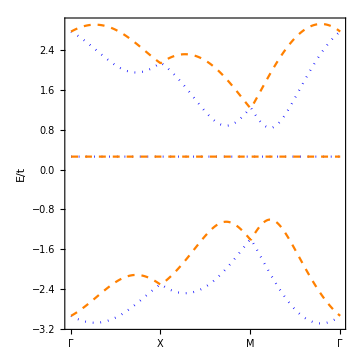

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},U=0.5, fil=3.0, β=100,krange=25},ListPlot[Table[ PlotMFDisp[bsp,U,fil,β,krange][[All,i]],{i,1,6,1}],PlotStyle->{{Blue,Dotted},{Orange,Dashed}},
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean-Field Magnetization

```mathematica
Clear[Magn];Magn[bsp_,U_, fil_,β_,krange_,orb_]:=  Magn[bsp,U,fil,β,krange,orb]=Module[{itrMF=FullSoln[bsp,U,fil,β,krange][[2]]},{1/2( itrMF[[orb+6]] + itrMF[[orb+9]]),1/(2I)( itrMF[[orb+6]] - itrMF[[orb+9]]), 1/2( itrMF[[orb+3]] - itrMF[[orb]])}];
```

```mathematica
Clear[Density];Density[bsp_,U_, fil_,β_,krange_]:= Density[bsp,U,fil,β,krange]=  Module[{itrMF=ItrFnMF[bsp,U,fil,β,krange][[2]]},Total[ itrMF[[1;;6]]] ];
```

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[Density[bsp,U,fil,β,krange],{U,0,10},PlotRange->All]]
```

$Aborted

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[Norm[Total[Table[Magn[bsp,U,fil,β,krange,i],{i,1,3}]]],{U,0,4,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A+S_B+S_C>"},FrameLabel->{"U/t","<S>"}]]
```

$Aborted

```mathematica
?Magn
```

```mathematica
Rasterize[Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,10,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"},FrameLabel->{"U/t","<S>"}]],ImageResolution->300]
```

-Graphics-

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},Table[{U,Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,10,0.1}]]
```

{{0.,1.26987×10^-16,8.38511×10^-17,1.13802×10^-16},{0.1,1.52298×10^-13,7.16175×10^-13,6.4452×10^-13},{0.2,1.54096×10^-13,2.31842×10^-13,1.99378×10^-13},{0.3,9.45221×10^-11,1.96201×10^-10,5.96432×10^-11},{0.4,5.30702×10^-10,6.5183×10^-10,7.10283×10^-10},{0.5,3.50331×10^-10,3.74774×10^-10,5.49581×10^-10},{0.6,1.32024×10^-9,1.10087×10^-9,1.20912×10^-9},{0.7,7.80944×10^-8,4.68567×10^-8,1.1683×10^-7},{0.8,1.81689×10^-8,1.18451×10^-8,2.12413×10^-8},{0.9,0.0197862,0.237844,0.221782},{1.,7.01482×10^-8,4.81021×10^-8,1.01724×10^-7},{1.1,0.0000140608,0.0000160271,3.8372×10^-6},{1.2,0.0295793,0.249382,0.230346},{1.3,0.0332153,0.253242,0.233716},{1.4,6.38015×10^-7,8.25901×10^-7,9.73231×10^-8},{1.5,0.0000205605,5.4199×10^-6,0.000019233},{1.6,0.0000932686,0.0000277572,0.0000668849},{1.7,0.0500761,0.266625,0.246726},{1.8,4.69204×10^-6,3.75613×10^-6,1.6908×10^-6},{1.9,0.0595442,0.273761,0.254314},{2.,0.0668117,0.280695,0.258342},{2.1,0.0722251,0.283778,0.262612},{2.2,0.0000497053,0.0000289746,0.0000201575},{2.3,0.000132799,0.0000623743,0.0000661285},{2.4,0.000103325,0.0000318847,0.0000723155},{2.5,0.000064979,0.00001469,0.0000427863},{2.6,0.000169838,0.0000584006,0.0000885528},{2.7,0.12263,0.316346,0.290705},{2.8,0.127111,0.312325,0.296678},{2.9,0.0186693,0.0033196,0.00367133},{3.,0.00682803,0.0011455,0.00109346},{3.1,0.0000489351,8.99337×10^-7,1.7567×10^-6},{3.2,6.7285×10^-16,5.80178×10^-17,2.22436×10^-16},{3.3,0.202368,0.358965,0.329967},{3.4,0.174267,0.341621,0.331138},{3.5,0.227003,0.374956,0.341003},{3.6,0.00896883,0.00223667,0.00347756},{3.7,0.0539323,0.0155012,0.0167777},{3.8,0.,0.,0.},{3.9,0.,0.,0.},{4.,0.,0.,0.},{4.1,0.282491,0.400127,0.375802},{4.2,0.287797,0.397484,0.382612},{4.3,0.0277274,0.00193871,0.00302666},{4.4,0.274779,0.394655,0.376547},{4.5,0.319858,0.0267123,0.0351092},{4.6,0.318758,0.416691,0.397578},{4.7,0.,0.,0.},{4.8,0.,0.,0.},{4.9,0.0602177,0.42505,0.433497},{5.,0.,0.,0.},{5.1,0.0531312,0.43076,0.439164},{5.2,0.0680601,0.441325,0.45102},{5.3,0.345108,0.427886,0.413963},{5.4,0.,0.,0.},{5.5,0.,0.,0.},{5.6,0.0613578,0.451399,0.458385},{5.7,0.,0.,0.},{5.8,0.0354004,0.448993,0.45113},{5.9,0.0551401,0.456395,0.461874},{6.,0.,0.,0.},{6.1,0.0385348,0.456524,0.458587},{6.2,0.,0.,0.},{6.3,0.,0.,0.},{6.4,0.,0.,0.},{6.5,0.0466486,0.465172,0.468483},{6.6,0.,0.,0.},{6.7,0.,0.,0.},{6.8,0.0362552,0.466649,0.469522},{6.9,0.,0.,0.},{7.,0.,0.,0.},{7.1,0.0383532,0.470989,0.473249},{7.2,0.0317257,0.47839,0.479733},{7.3,0.,0.,0.},{7.4,0.0362733,0.473789,0.475501},{7.5,0.,0.,0.},{7.6,0.,0.,0.},{7.7,0.,0.,0.},{7.8,0.0207185,0.000537182,0.332453},{7.9,0.,0.,0.},{8.,0.023253,0.482416,0.48273},{8.1,0.,0.,0.},{8.2,0.,0.,0.},{8.3,0.,0.,0.},{8.4,0.491762,0.492804,0.498472},{8.5,0.0171032,0.473808,0.477122},{8.6,0.0274695,0.481063,0.482084},{8.7,0.,0.,0.},{8.8,0.457302,0.475212,0.480591},{8.9,0.,0.,0.},{9.,0.0192263,0.476623,0.48176},{9.1,0.0183783,0.475281,0.481896},{9.2,0.,0.,0.},{9.3,0.,0.,0.},{9.4,0.,0.,0.},{9.5,0.,0.,0.},{9.6,0.,0.,0.},{9.7,0.,0.,0.},{9.8,0.0202068,0.485572,0.486147},{9.9,0.,0.,0.},{10.,0.,0.,0.}}

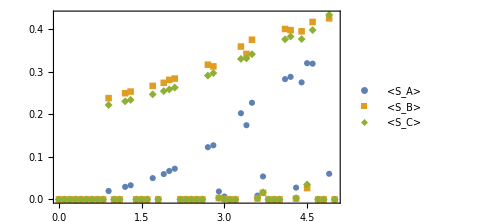

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,5,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"}]]
```

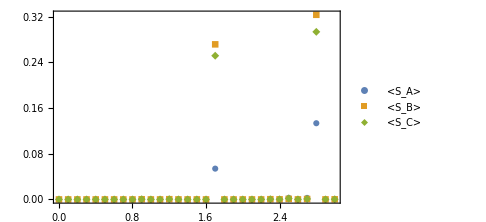

$Aborted

```mathematica
Block[ {bsp={{0.45,0.0},{0.2,0.2},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,3,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"}]]
```